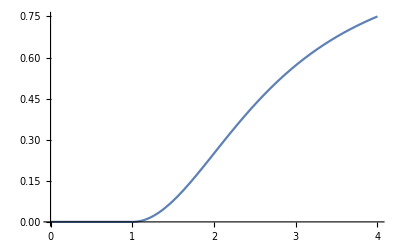

```mathematica
n=2;
A0 = 1;
f[A_] := Piecewise[{{(A/A0-1)^n/(3+(A/A0-1)^n),A>A0},{0,A<A0}}]
Plot[f[A],{A,0,4}]
```